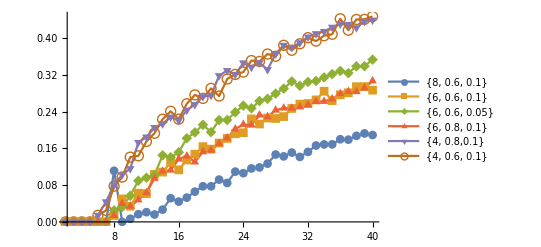

```mathematica
ListPlot[{ttb[[2]],llb[[2]], bbb[[2]], ccb[[2]], ddb[[2]], eeb[[2]]}, Joined->True, PlotRange->{{2, 40}, Full}, PlotMarkers->Automatic, PlotLegends->{"{8, 0.6, 0.1}", "{6, 0.6, 0.1}", "{6, 0.6, 0.05}", "{6, 0.8, 0.1}", "{4, 0.8,0.1}", "{4, 0.6, 0.1}"}]
```

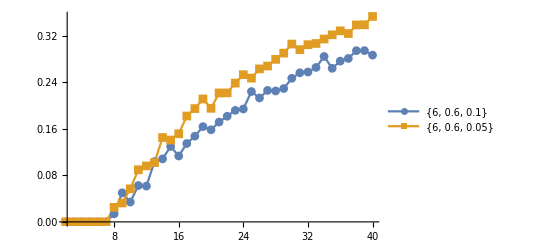

```mathematica
ListPlot[{llb[[2]], bbb[[2]]}, Joined->True, PlotRange->{{2, 40}, Full}, PlotMarkers->Automatic, PlotLegends->{"{6, 0.6, 0.1}", "{6, 0.6, 0.05}"}]
```

```mathematica
ListPlot[{ttb[[2]],llb[[2]], bbb[[2]], ccb[[2]], ddb[[2]], eeb[[2]]}, Joined->True, PlotRange->{{2, 40}, Full}, PlotMarkers->Automatic, PlotLegends->{"{8, 0.6, 0.1}", "{6, 0.6, 0.1}", "{6, 0.6, 0.05}", "{6, 0.8, 0.1}", "{4, 0.8,0.1}", "{4, 0.6, 0.1}"}]
```

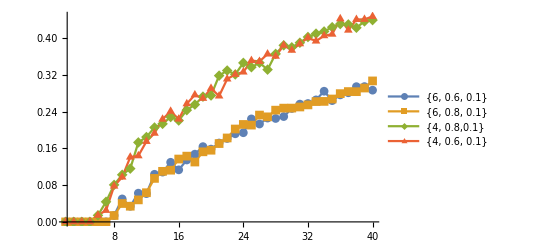

```mathematica
ListPlot[{llb[[2]],  ccb[[2]], ddb[[2]], eeb[[2]]}, Joined->True, PlotRange->{{2, 40}, Full}, PlotMarkers->Automatic, PlotLegends->{ "{6, 0.6, 0.1}",  "{6, 0.8, 0.1}", "{4, 0.8,0.1}", "{4, 0.6, 0.1}"}]
```

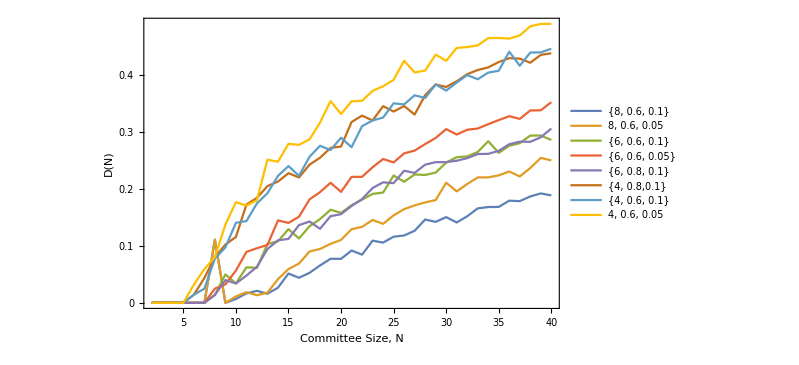

```mathematica
ListPlot[
{ttb[[2]], wwb[[2]],llb[[2]], bbb[[2]], ccb[[2]], ddb[[2]], eeb[[2]], ggb[[2]]}, Joined->True, PlotRange->{{2, 40}, Full}, PlotLegends->Placed[{"{8, 0.6, 0.1}","8, 0.6, 0.05", "{6, 0.6, 0.1}", "{6, 0.6, 0.05}", "{6, 0.8, 0.1}", "{4, 0.8,0.1}", "{4, 0.6, 0.1}", "4, 0.6, 0.05"}, {Left,Top}],
FrameLabel->{"Committee Size, N", "D(N)"}, LabelStyle->{Black, 15},
Frame->{{True, None}, {True, None}}, FrameTicks->{{{0, 0.1, 0.2, 0.3, 0.4}, None}, {{5,10,15,20,25,30,35,40}, None}}
]
```

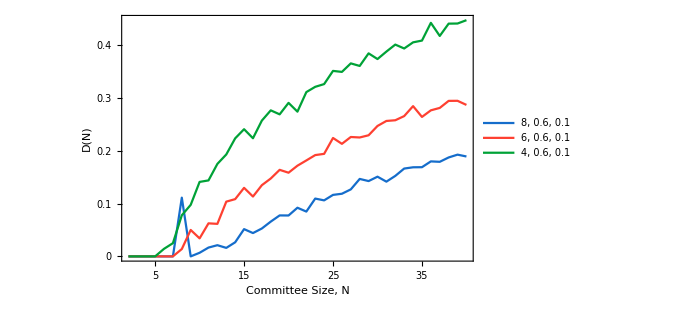

```mathematica
ListPlot[
{ttb[[2]],llb[[2]], eeb[[2]]}, Joined->True, PlotRange->{{2, 40}, Full}, PlotLegends->Placed[{"8, 0.6, 0.1", "6, 0.6, 0.1", "4, 0.6, 0.1"}, {Left,Top}], 
FrameLabel->{"Committee Size, N", "D(N)"}, LabelStyle->{Black, 18, FontFamily->"Latin Modern Roman"},
Frame->{{True, None}, {True, None}}, FrameTicks->{{{0, 0.1, 0.2, 0.3, 0.4}, None}, {{5,10,15,20,25,30,35,40}, None}},
PlotStyle-> {blue, red, green},
ImageSize->{500, 350}
]
```

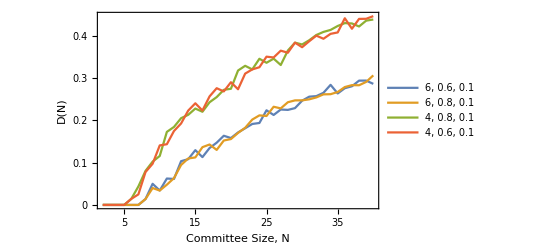

```mathematica
ListPlot[
{llb[[2]],  ccb[[2]], ddb[[2]], eeb[[2]]}, Joined->True, PlotRange->{{2, 40}, Full},PlotLegends->Placed[{ "6, 0.6, 0.1",  "6, 0.8, 0.1", "4, 0.8, 0.1", "4, 0.6, 0.1"}, {Left, Top}],
FrameLabel->{"Committee Size, N", "D(N)"}, LabelStyle->{Black, 15},
Frame->{{True, None}, {True, None}}, FrameTicks->{{{0, 0.1, 0.2, 0.3, 0.4}, None}, {{5,10,15,20,25,30,35,40}, None}}
]
```

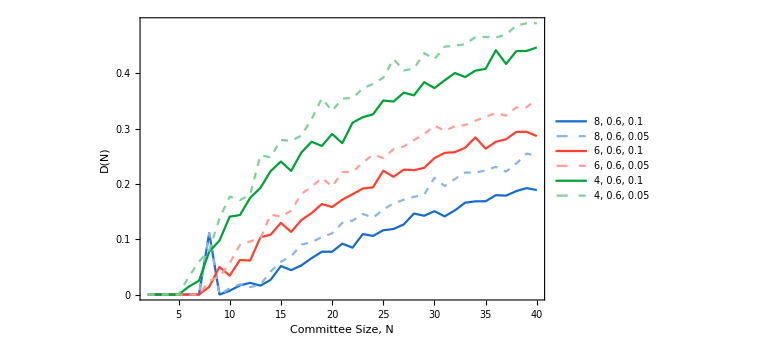

```mathematica
ListPlot[
{ttb[[2]], wwb[[2]],llb[[2]], bbb[[2]], eeb[[2]],ggb[[2]]}, Joined->True, PlotRange->{{2, 40}, Full}, PlotLegends->Placed[{Style["8, 0.6, 0.1",15], Style["8, 0.6, 0.05",15],Style["6, 0.6, 0.1",15], Style["6, 0.6, 0.05",15], Style["4, 0.6, 0.1",15], Style["4, 0.6, 0.05",15]}, {Left,Top}],
FrameLabel->{"Committee Size, N", "D(N)"}, LabelStyle->{Black, 18, FontFamily->"Latin Modern Roman"},
Frame->{{True, None}, {True, None}}, FrameTicks->{{{0, 0.1, 0.2, 0.3, 0.4}, None}, {{5,10,15,20,25,30,35,40}, None}},
PlotStyle-> {blue, {Dashed,Lighter[blue,0.5]}, red, {Dashed,Lighter[red, 0.5]}, green, {Dashed,Lighter[green, 0.5]}}
]
```

```mathematica
blue = RGBColor[21/256,109/256,204/256]
red = RGBColor[255/256,64/256,49/256]
green = RGBColor[0/256,163/256,55/256]
```

RGBColor[Rational[21, 256], Rational[109, 256], Rational[51, 64]]

RGBColor[Rational[255, 256], Rational[1, 4], Rational[49, 256]]

RGBColor[0, Rational[163, 256], Rational[55, 256]]

```mathematica
,0.5
```

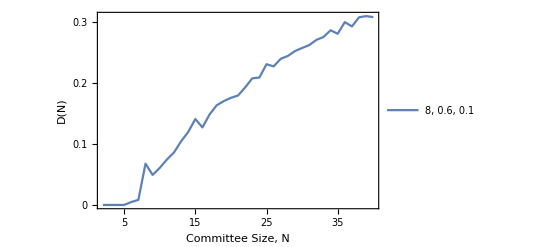

```mathematica
ListPlot[
Mean[{ttb[[2]],llb[[2]], eeb[[2]]}], 
Joined->True, 
PlotRange->{{2, 40}, Full}, 
PlotLegends->Placed[{"8, 0.6, 0.1"}, {Left, Top}], 
FrameLabel->{"Committee Size, N", "D(N)"}, LabelStyle->{Black, 15},
Frame->{{True, None}, {True, None}}, FrameTicks->{{{0, 0.1, 0.2, 0.3, 0.4}, None}, {{5,10,15,20,25,30,35,40}, None}}
]
```

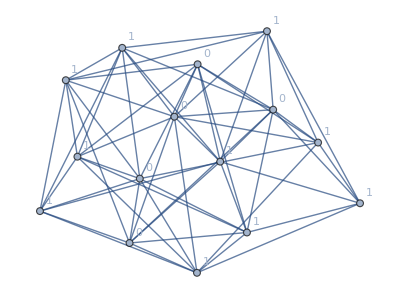

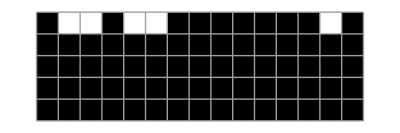
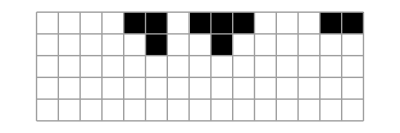
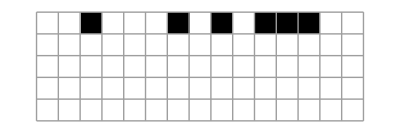
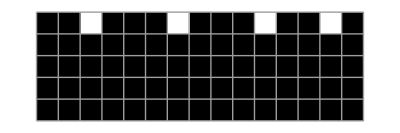
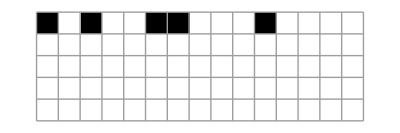
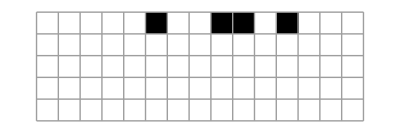
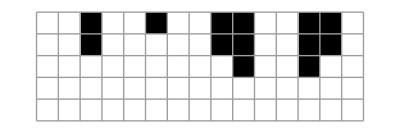

```mathematica
grapher[15, 8, 0.1]
```

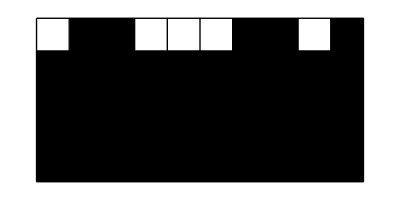
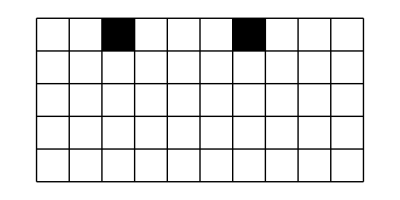
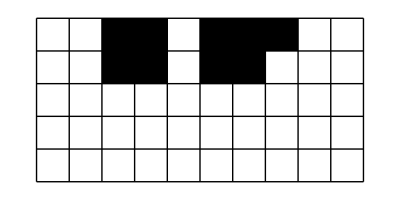
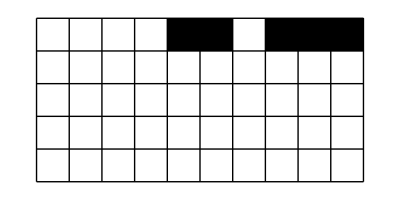
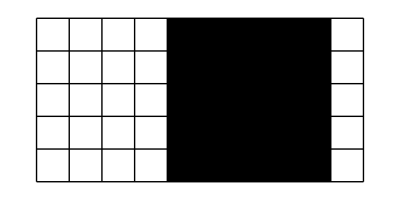
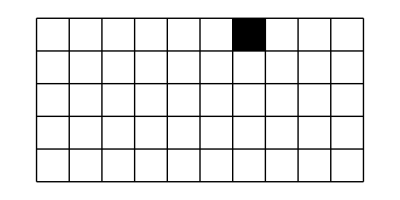
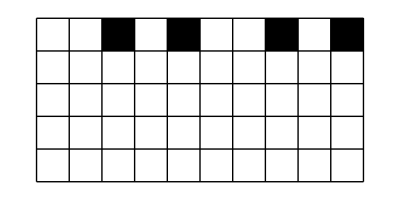
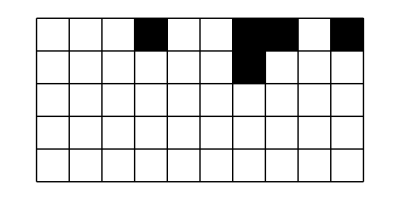

```mathematica
Table[plotter[modeler[10, {8, 0.6, 0.1}, 4]], 10]
Table[plotter[modeler[20, {8, 0.6, 0.1}, 4]], 10]
Table[plotter[modeler[30, {8, 0.6, 0.1}, 4]], 10]
Table[plotter[modeler[40, {8, 0.6, 0.1}, 4]], 10]
```

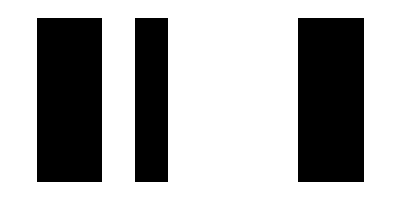
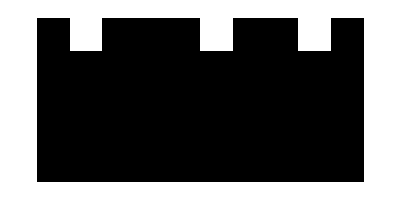
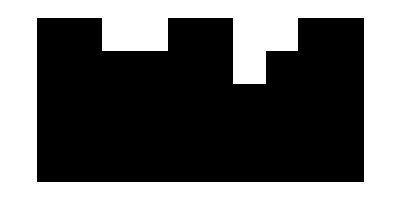
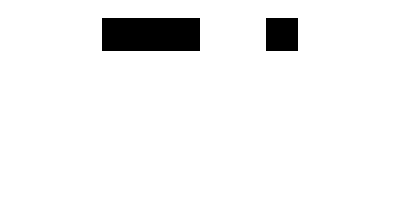
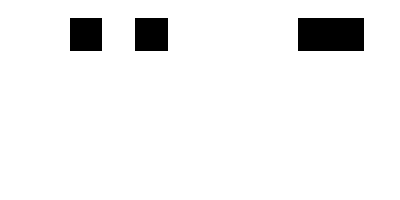

```mathematica
Table[plotter[modeler[10, {8, 0.6, 0.1}, 4]], 5]
```

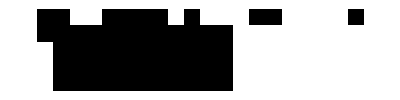
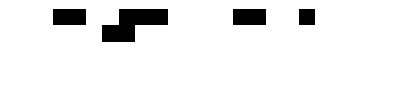
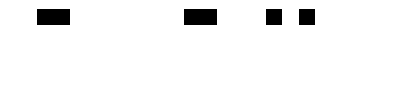
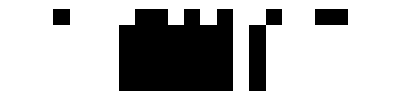
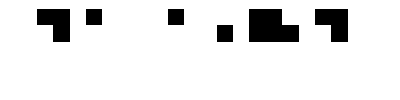

```mathematica
Table[plotter[modeler[20, {8, 0.6, 0.1}, 4]], 5]
```

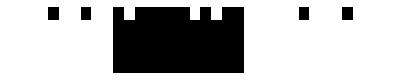
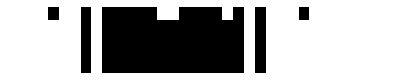
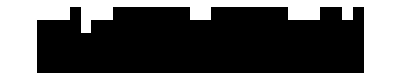
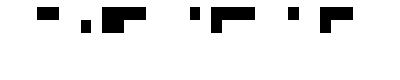
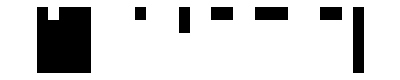

```mathematica
Table[plotter[modeler[30, {8, 0.6, 0.1}, 4]], 5]
```

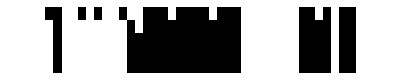
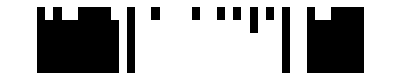
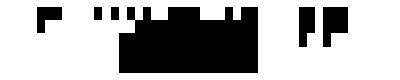
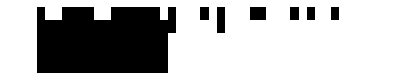
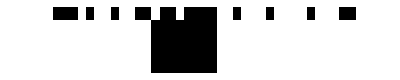

```mathematica
Table[plotter[modeler[40, {8, 0.6, 0.1}, 4]], 5]
```

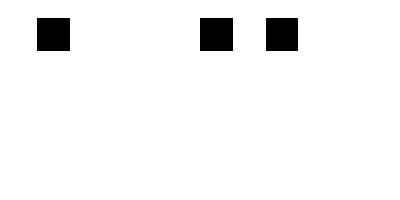
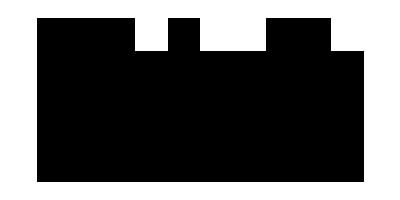
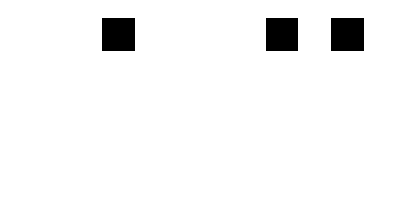
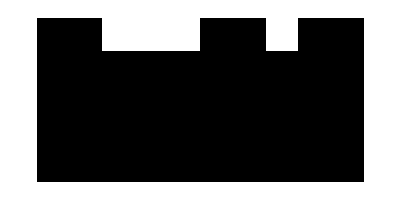
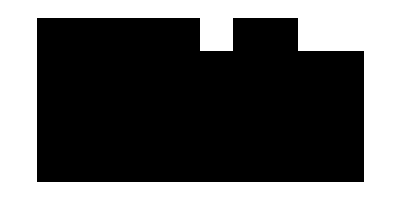

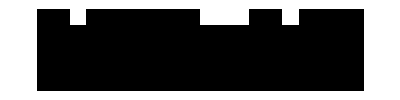
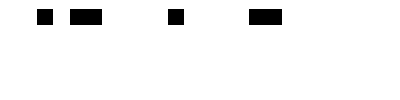
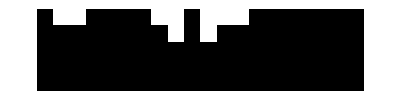

```mathematica
Table[plotter[modeler[10, {8, 0.6, 0.1}, 4]], 5]
Table[plotter[modeler[20, {8, 0.6, 0.1}, 4]], 5]
Table[plotter[modeler[30, {8, 0.6, 0.1}, 4]], 5]
Table[plotter[modeler[40, {8, 0.6, 0.1}, 4]], 5]
```